# O(𝒩) model

## Wick function setup

```mathematica
SetAttributes[δ,{Orderless}]
SetAttributes[Δ,{Orderless}]
```

```mathematica
Clear[AngleBracket,CenterDot];
⟨CenterDot[x__ϕ]⟩:=∑_(ι=2)^Length[{x}] ⟨{x}⟦1⟧·{x}⟦ι⟧⟩ ⟨CenterDot@@Drop[{x}⟦2;;All⟧,{ι-1}]⟩/;Length[{x}]>2;
⟨CenterDot[ϕ[x__]]⟩:=ϕ[x]
⟨ϕ[i_,x_]·ϕ[j_,y_]⟩:=δ[i,j]Δ[x,y]
```

```mathematica
Clear[ΔToGraph,GraphToΔ,SumRule,IsomorphicDiagramQ,AmputatedDiagramQ,GatherDiagrams,UndEdgesRule]
ΔToGraph:=List@@ExpandAll[#]/.{v___ (Longest[b__])?(MatchQ[Δ[__]^(p_.)]):>{Graph[Flatten[List[b]/.{Δ[α__]^q_:>ConstantArray[Δ[α],q]}]/.{Δ->UndirectedEdge}],Times[v]}}&
GraphToΔ:=Total@*Map[Last[#]Times@@(Δ@@@EdgeList[First@#])&];
SumRule[intP_]:=ExpandAll[#]//.{
δ[α_,β_]Longest[γ_].. :>(γ/.β->α)/;!FreeQ[β,intP]&&!FreeQ[γ,β],δ[α_,β_]^2 Longest[γ_]..:>𝒩(γ/.β->α)/;!FreeQ[{α,β},intP]&&FreeQ[γ,β],δ[α_,α_]:>𝒩/;!FreeQ[α,intP]
}&;
UndEdgesRule=(α_<->β_):>(β<->α)/;OrderedQ[{β,α}];
IsomorphicDiagramQ[intP_]:=Function[{x,y},(EdgeList[y]/.(Thread[(List@@intP)->#]&/@Permutations[List@@intP])//.UndEdgesRule)//Map[ContainsExactly[EdgeList[x]//.UndEdgesRule,#]&]//Apply[Or]]
GatherDiagrams[intP_]:=Association@*Map[Graph[#1⟦1,1⟧,VertexLabels->Thread[Complement[VertexList[#1⟦1,1⟧],List@@intP]->Automatic]]->Simplify@Total[#1⟦All,2⟧]&]@*(Gather[#,IsomorphicDiagramQ[intP][First@#1,First@#2]&]&)
AmputatedDiagramQ[intP_]:=KEdgeConnectedGraphQ[Graph@DeleteCases[α_<->β_/;FreeQ[α,intP]⊻FreeQ[β,intP]]@EdgeList[#1],2]&
```

## 𝒪(λ^1) using Wick (vertex)

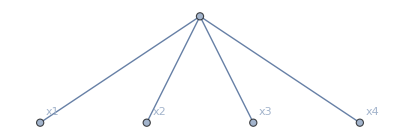
<|-Graphics-→-ⅈ λ (i,l j,k+i,k j,l+i,j k,l)|>

```mathematica
FourPointConnected1st=(-I λ)/8⟨ϕ[i,x1]·ϕ[j,x2]·ϕ[k,x3]·ϕ[l,x4]·ϕ[p,z]·ϕ[p,z]·ϕ[q,z]·ϕ[q,z]⟩//SumRule[p|q]// ΔToGraph//Select[WeaklyConnectedGraphQ[First@#]&]//GatherDiagrams[{z}]//Map[#/.δ->KroneckerDelta&]
```

```mathematica
GraphToΔ@KeyValueMap[List]@FourPointConnected1st//Collect[Expand@#/.δ->KroneckerDelta,(Δ[__]..),Highlighted@*Simplify]&
```

-ⅈ λ (i,l j,k+i,k j,l+i,j k,l) Δ[x1,z] Δ[x2,z] Δ[x3,z] Δ[x4,z]

## 𝒪(λ^2) using Wick

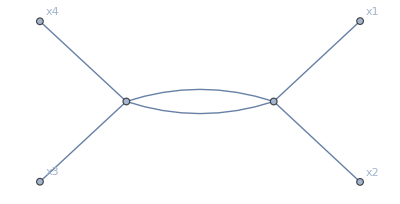
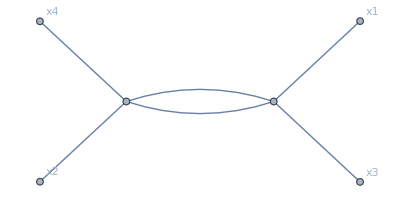
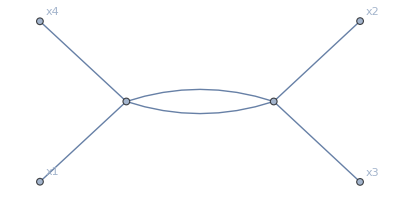
<|-Graphics-→-1/2 λ^2 (2 i,l j,k+2 i,k j,l+(4+𝒩) i,j k,l),-Graphics-→-1/2 λ^2 (2 i,l j,k+(4+𝒩) i,k j,l+2 i,j k,l),-Graphics-→-1/2 λ^2 ((4+𝒩) i,l j,k+2 (i,k j,l+i,j k,l))|>

```mathematica
FourPointConnected2nd=1/2((-I λ)/8)^2⟨ϕ[i,x1]·ϕ[j,x2]·ϕ[k,x3]·ϕ[l,x4]·ϕ[p,z]·ϕ[p,z]·ϕ[q,z]·ϕ[q,z]·ϕ[r,w]·ϕ[r,w]·ϕ[s,w]·ϕ[s,w]⟩//SumRule[r|s|p|q]//ΔToGraph//Select[WeaklyConnectedGraphQ[First@#]&&AmputatedDiagramQ[z|w][First@#]&]//GatherDiagrams[z|w]//Map[#/.δ->KroneckerDelta&]
```

```mathematica
GraphToΔ@KeyValueMap[List]@FourPointConnected2nd//Collect[Expand@#/.δ->KroneckerDelta,Δ[w,z]^(p_.)(Δ[__]..),Highlighted@*Simplify]&
```

-1/2 λ^2 (2 i,l j,k+2 i,k j,l+(4+𝒩) i,j k,l) Δ[w,x3] Δ[w,x4] Δ[w,z]^2 Δ[x1,z] Δ[x2,z]+-1/2 λ^2 (2 i,l j,k+(4+𝒩) i,k j,l+2 i,j k,l) Δ[w,x2] Δ[w,x4] Δ[w,z]^2 Δ[x1,z] Δ[x3,z]+-1/2 λ^2 ((4+𝒩) i,l j,k+2 (i,k j,l+i,j k,l)) Δ[w,x1] Δ[w,x4] Δ[w,z]^2 Δ[x2,z] Δ[x3,z]

## 𝒪(λ^3) using Wick

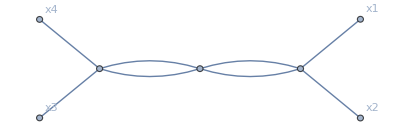
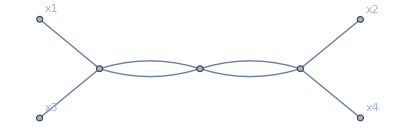
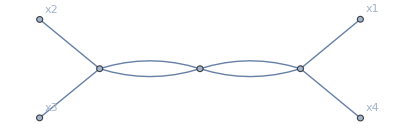
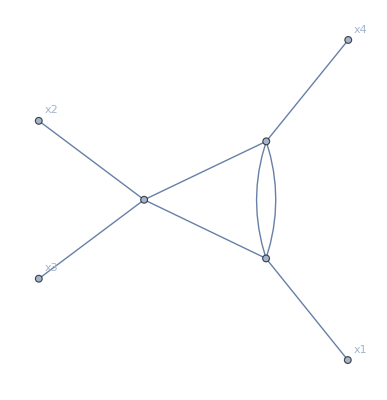
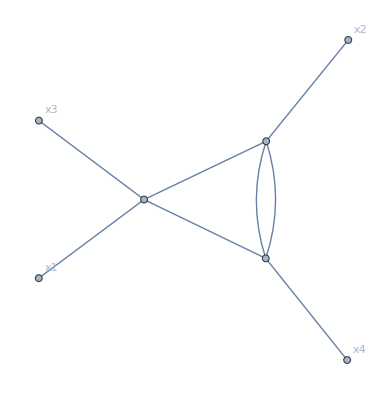
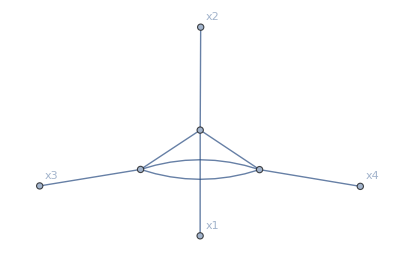
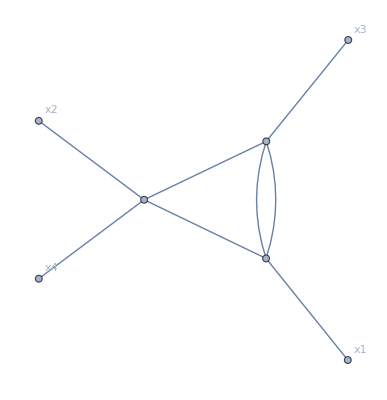
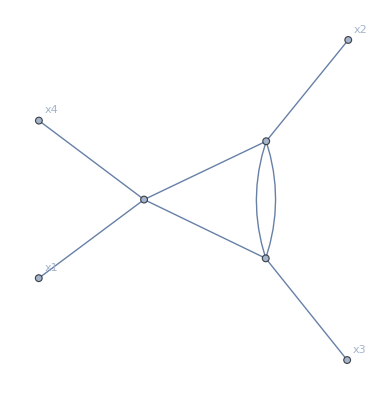
<|-Graphics-→1/4 ⅈ λ^3 (4 i,l j,k+4 i,k j,l+(12+6 𝒩+𝒩^2) i,j k,l),-Graphics-→1/4 ⅈ λ^3 (4 i,l j,k+(12+6 𝒩+𝒩^2) i,k j,l+4 i,j k,l),-Graphics-→1/4 ⅈ λ^3 ((12+6 𝒩+𝒩^2) i,l j,k+4 (i,k j,l+i,j k,l)),-Graphics-→1/2 ⅈ λ^3 ((10+3 𝒩) i,l j,k+(6+𝒩) (i,k j,l+i,j k,l)),-Graphics-→1/2 ⅈ λ^3 ((6+𝒩) i,l j,k+(10+3 𝒩) i,k j,l+(6+𝒩) i,j k,l),-Graphics-→1/2 ⅈ λ^3 ((6+𝒩) i,l j,k+(6+𝒩) i,k j,l+(10+3 𝒩) i,j k,l),-Graphics-→1/2 ⅈ λ^3 ((6+𝒩) i,l j,k+(10+3 𝒩) i,k j,l+(6+𝒩) i,j k,l),-Graphics-→1/2 ⅈ λ^3 ((10+3 𝒩) i,l j,k+(6+𝒩) (i,k j,l+i,j k,l)),-Graphics-→1/2 ⅈ λ^3 ((6+𝒩) i,l j,k+(6+𝒩) i,k j,l+(10+3 𝒩) i,j k,l),-Graphics-→1/2 ⅈ (2+𝒩) λ^3 (2 i,l j,k+2 i,k j,l+(4+𝒩) i,j k,l),-Graphics-→1/2 ⅈ (2+𝒩) λ^3 (2 i,l j,k+(4+𝒩) i,k j,l+2 i,j k,l),-Graphics-→1/2 ⅈ (2+𝒩) λ^3 ((4+𝒩) i,l j,k+2 (i,k j,l+i,j k,l))|>

```mathematica
FourPointConnected3rd=1/6((-I λ)/8)^3⟨ϕ[i,x1]·ϕ[j,x2]·ϕ[k,x3]·ϕ[l,x4]·ϕ[p,z]·ϕ[p,z]·ϕ[q,z]·ϕ[q,z]·ϕ[r,w]·ϕ[r,w]·ϕ[s,w]·ϕ[s,w]·ϕ[t,y]·ϕ[t,y]·ϕ[u,y]·ϕ[u,y]⟩//SumRule[r|s|p|q|t|u]//ΔToGraph//Select[WeaklyConnectedGraphQ[First@#]&&AmputatedDiagramQ[z|w|y][First@#]&]//GatherDiagrams[z|w|y]//Map[#/.δ->KroneckerDelta&]
```

```mathematica
GraphToΔ@KeyValueMap[List]@FourPointConnected3rd//Collect[Expand@#/.δ->KroneckerDelta,Δ[w,z]^(p_.)(Δ[__]..),Highlighted@*Simplify]&
```

1/4 ⅈ λ^3 (4 i,l j,k+4 i,k j,l+(12+6 𝒩+𝒩^2) i,j k,l) Δ[w,y]^2 Δ[w,z]^2 Δ[x1,z] Δ[x2,z] Δ[x3,y] Δ[x4,y]+1/4 ⅈ λ^3 (4 i,l j,k+(12+6 𝒩+𝒩^2) i,k j,l+4 i,j k,l) Δ[w,y]^2 Δ[w,z]^2 Δ[x1,z] Δ[x2,y] Δ[x3,z] Δ[x4,y]+1/4 ⅈ λ^3 ((12+6 𝒩+𝒩^2) i,l j,k+4 (i,k j,l+i,j k,l)) Δ[w,y]^2 Δ[w,z]^2 Δ[x1,y] Δ[x2,z] Δ[x3,z] Δ[x4,y]+1/2 ⅈ λ^3 ((10+3 𝒩) i,l j,k+(6+𝒩) (i,k j,l+i,j k,l)) Δ[w,x4] Δ[w,y] Δ[w,z]^2 Δ[x1,z] Δ[x2,y] Δ[x3,y] Δ[y,z]+1/2 ⅈ λ^3 ((6+𝒩) i,l j,k+(10+3 𝒩) i,k j,l+(6+𝒩) i,j k,l) Δ[w,x4] Δ[w,y] Δ[w,z]^2 Δ[x1,y] Δ[x2,z] Δ[x3,y] Δ[y,z]+1/2 ⅈ λ^3 ((6+𝒩) i,l j,k+(6+𝒩) i,k j,l+(10+3 𝒩) i,j k,l) Δ[w,y]^2 Δ[w,x4] Δ[w,z] Δ[x1,z] Δ[x2,z] Δ[x3,y] Δ[y,z]+1/2 ⅈ λ^3 ((6+𝒩) i,l j,k+(10+3 𝒩) i,k j,l+(6+𝒩) i,j k,l) Δ[w,x3] Δ[w,y] Δ[w,z]^2 Δ[x1,z] Δ[x2,y] Δ[x4,y] Δ[y,z]+1/2 ⅈ λ^3 ((10+3 𝒩) i,l j,k+(6+𝒩) (i,k j,l+i,j k,l)) Δ[w,x3] Δ[w,y] Δ[w,z]^2 Δ[x1,y] Δ[x2,z] Δ[x4,y] Δ[y,z]+1/2 ⅈ λ^3 ((6+𝒩) i,l j,k+(6+𝒩) i,k j,l+(10+3 𝒩) i,j k,l) Δ[w,x2] Δ[w,y] Δ[w,z]^2 Δ[x1,z] Δ[x3,y] Δ[x4,y] Δ[y,z]+1/2 ⅈ (2+𝒩) λ^3 (2 i,l j,k+2 i,k j,l+(4+𝒩) i,j k,l) Δ[w,w] Δ[w,y] Δ[w,z] Δ[x1,z] Δ[x2,z] Δ[x3,y] Δ[x4,y] Δ[y,z]+1/2 ⅈ (2+𝒩) λ^3 (2 i,l j,k+(4+𝒩) i,k j,l+2 i,j k,l) Δ[w,w] Δ[w,y] Δ[w,z] Δ[x1,z] Δ[x2,y] Δ[x3,z] Δ[x4,y] Δ[y,z]+1/2 ⅈ (2+𝒩) λ^3 ((4+𝒩) i,l j,k+2 (i,k j,l+i,j k,l)) Δ[w,w] Δ[w,y] Δ[w,z] Δ[x1,y] Δ[x2,z] Δ[x3,z] Δ[x4,y] Δ[y,z]

## 𝒪(λ^2) using Feynman rules

```mathematica
Clear[Propagator,Vertexλ]
Propagator[{i_,x_},{j_,y_}]=δ[i,j]Δ[x,y];
Vertexλ[{i_,j_,l_,k_}]=-ⅈ λ (δ[i,l] δ[j,k]+δ[i,k] δ[j,l]+δ[i,j] δ[k,l]);
AllChannels[{x1_,x2_,x3_,x4_}]=Total[#/.{Thread[{x1,x2,x3,x4}->{x1,x2,x3,x4}],Thread[{x1,x2,x3,x4}->{x1,x3,x4,x2}],Thread[{x1,x2,x3,x4}->{x1,x4,x2,x3}]}]&;
```

```mathematica
1/2 Propagator[{i,x1},{i0,z}]Propagator[{j,x2},{j0,z}]Vertexλ[{i0,j0,p1,q1}]Propagator[{p1,z},{p2,w}]Propagator[{q1,z},{q2,w}]Vertexλ[{p2,q2,k0,l0}]Propagator[{k0,w},{k,x3}]Propagator[{l0,w},{l,x4}]//AllChannels[{x1,x2,x3,x4}]//SumRule[i0|j0|k0|l0|p1|p2|q1|q2]//Collect[Expand@#/.δ->KroneckerDelta,Δ[w,z]^(p_.)(Δ[__]..),Highlighted@*Simplify]&
```

-1/2 λ^2 (2 i,l j,k+2 i,k j,l+(4+𝒩) i,j k,l) Δ[w,x3] Δ[w,x4] Δ[w,z]^2 Δ[x1,z] Δ[x2,z]+-1/2 λ^2 (2 i,l j,k+2 i,k j,l+(4+𝒩) i,j k,l) Δ[w,x2] Δ[w,x4] Δ[w,z]^2 Δ[x1,z] Δ[x3,z]+-1/2 λ^2 (2 i,l j,k+2 i,k j,l+(4+𝒩) i,j k,l) Δ[w,x2] Δ[w,x3] Δ[w,z]^2 Δ[x1,z] Δ[x4,z]